### Building the Hamiltonian

```mathematica
bsize=20;ω0=1.0;
(*Two level system initial Hamiltonian*)
H0TSS=SparseArray[Band[{1,1}]->{-ω0/2,ω0/2}];
(*QHO Hamiltonian*)
H0HO=SparseArray[Band[{1,1}]->Table[n+1/2,{n,0,bsize-1}]];
σp={{0,0},{1,0}};
σm={{0,1},{0,0}};
σx = σp + σm

(*Annihilation operator definition*)
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}]; 

(*We have to choose a convention, i.e., the TSS is on the left in tensor producs, while the HO is on the right*)
H0=KroneckerProduct[IdentityMatrix[2],H0HO]+KroneckerProduct[H0TSS,IdentityMatrix[bsize]]; (* Scaling via tensor product *)

(*The coupling terms*)
j = 0.1;
Hcoup=j(KroneckerProduct[σx,a]+KroneckerProduct[σx,a†]);
Htot=H0+Hcoup;
```

{{0,1},{1,0}}

### Initial state

```mathematica
ψ0[w_,x0_]=1/Sqrt[Sqrt[ π]w] Exp[-(x-x0)^2/(2 w^2)];(*Define initial Gaussian state*)
EigState[n_, x_]=π^(-1/4)/Sqrt[2^n n!] Exp[-x^2/2]HermiteH[n,x];
coeff[n_,w_,x0_]:=NIntegrate[EigState[n, x]ψ0[w,x0],{x,-∞,∞},PrecisionGoal->6,AccuracyGoal->5]
ψ0HO=Table[coeff[n,1,2],{n,0,bsize-1}];

(*excited state in TSS and Gaussian in the QHO*)
ψ0Vec=KroneckerProduct[{0,1},ψ0HO]//Flatten;
```

### Build observable matrices

```mathematica
xM=KroneckerProduct[IdentityMatrix[2],1/Sqrt[2](a†+a)];(*Position of the oscillator*)
```

### Test the observable matrix

```mathematica
(*Expected x value for initial state*)
ConjugateTranspose[ψ0Vec].xM.ψ0Vec
xMSquared = xM . xM;
```

2.

```mathematica
2.0000000257064285
```

2.

### Propagate Initial State (position basis)

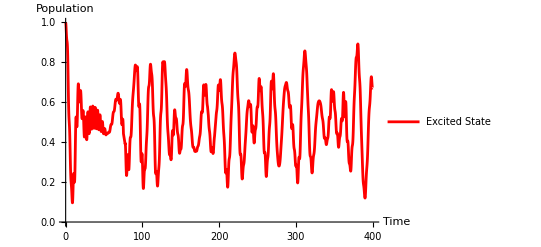

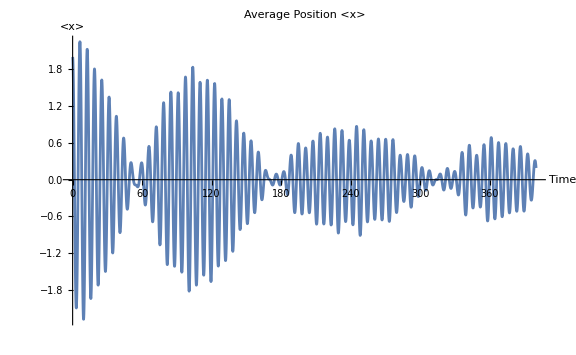

```mathematica
(* Define the time-evolved state vector *)
timeEvolutionOperator[t_] := MatrixExp[-I * Htot * t];
stateVector[t_] := timeEvolutionOperator[t] . ψ0Vec;

(* Compute expectation values *)
expectationValueX[t_]:=ConjugateTranspose[stateVector[t]].xM.stateVector[t];
expectationValueXSquared[t_]:=ConjugateTranspose[stateVector[t]].xMSquared.stateVector[t];

(*Tensor product with the QHO identity to get appropriately scaled operators*)
iqho=IdentityMatrix[bsize];
P1={{0,0},{0,1}}; (*Excited state projection operator*)
P1full=KroneckerProduct[P1,iqho];
populationExcited[t_]:=ConjugateTranspose[stateVector[t]].P1full.stateVector[t];

tMax =400; 

avgPositionPlotQHO = Plot[Re[expectationValueX[t]], {t, 0, tMax}, PlotLabel -> "Average Position <x>", AxesLabel -> {"Time", "<x>"}, PlotRange -> Full];
avgStatePlotTSS = Plot[{Re[populationExcited[t]]},{t,0,tMax},PlotLegends->{"Excited State"},AxesLabel->{"Time","Population"},PlotRange->{0,1}, PlotStyle->Red]

Show[avgPositionPlotQHO, PlotRange -> All, ImageSize -> Large]
```